```mathematica
strictupperbound[n_]:=n ⅇ(n/ⅇ)^n
```

```mathematica
strictlowerbound[n_]:=ⅇ(n/ⅇ)^n
```

```mathematica
stirling[n_]:=√(2π n)(n/ⅇ)^n
```

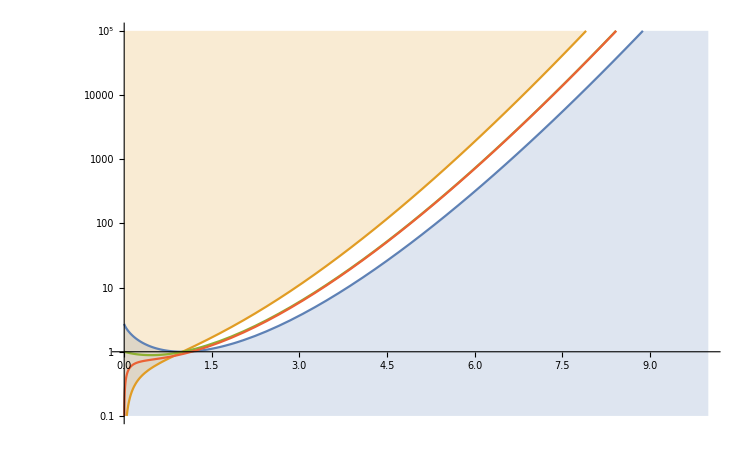

```mathematica
LogPlot[{strictlowerbound[n],strictupperbound[n],n!,stirling[n]},{n,0,10},ImageSize->750,Filling->{1->Bottom,2->Top},AxesOrigin->{0,0},PlotRange->{0.1,1*^5}]
```

```mathematica
ξ[α_]=Limit[(strictupperbound[n]/(strictlowerbound[α n]strictlowerbound[n-α n]))^(1/n),n->∞]
```

(1-α)^(-1+α) α^-α

```mathematica
Assuming[{n≥0,α≥0,α≤1},(strictupperbound[n]/(strictlowerbound[α n]strictlowerbound[n-α n]))//Simplify]
```

(n (1-α)^(n (-1+α)) α^(-n α))/ⅇ

```mathematica
Assuming[{n≥0,α≥0,α≤1},(strictupperbound[n]/(strictlowerbound[α n]strictlowerbound[n-α n]))/ξ[α]^n//Simplify]
```

n/ⅇ

```mathematica
Assuming[{n≥0,α≥0,α≤1},(stirling[n]/(stirling[α n]stirling[n-α n]))/ξ[α]^n//Simplify]
```

1/(√(2 π) √(-n (-1+α) α))

```mathematica
Assuming[{n≥1},Exp[Integrate[Log[x],{x,1,n}]+Log[n]]//Simplify]
```

ⅇ^(1-n) n^(1+n)

```mathematica
Assuming[{n≥1},Exp[Integrate[Log[x],{x,1,n}]]//Simplify]
```

ⅇ^(1-n) n^n

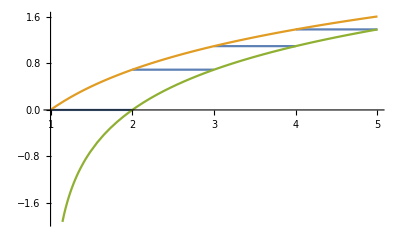

```mathematica
Plot[{Log[Floor[x]],Log[x],Log[x-1]},{x,1,5}]
```

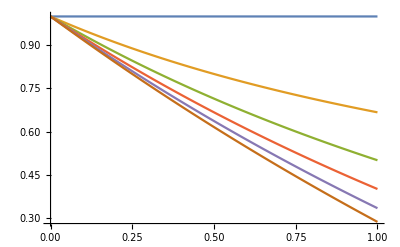

```mathematica
Plot[Evaluate@Table[(1+n+α-n α)/(1+n+α),{n,0,5}],{α,0,1}]
```

```mathematica
(1-α)^(-1+α) α^-α/.α->1/(η+1)//Simplify
```

(1/(1+η))^(-1/(1+η)) (η/(1+η))^(-1+1/(1+η))

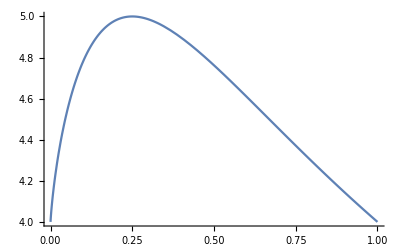

```mathematica
Plot[4^(1/(η+1))(1/(1+η))^(-1/(1+η)) (η/(1+η))^(-1+1/(1+η)),{η,0,1}]
```

```mathematica
Plot[4^(1/(η+1))((1+η)/η^(η/(η+1))),{η,0,1}]
```

-Graphics-

```mathematica
D[4^(1/(η+1))((1+η)/η^(η/(η+1))),η]//Simplify
```

-(4^(1/(1+η)) η^(-η/(1+η)) Log[4 η])/(1+η)

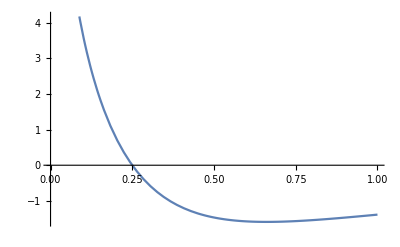

```mathematica
Plot[-(4^(1/(1+η)) η^(-η/(1+η)) Log[4 η])/(1+η),{η,0,1}]
```